# Курсовая работа

## Вариант 16

#### Загрузка данных

```mathematica
LogData = Flatten[Import["import_data_cupola.xlsx"],1];
data=Flatten[Import["import_hist_data.xlsx"],1];
```

```mathematica
rosn=Transpose[data][[1]];
gazp=Transpose[data][[2]];
sibn=Transpose[data][[3]];
ROSN=Transpose[LogData][[1]];
GAZP=Transpose[LogData][[2]];
SIBN=Transpose[LogData][[3]];
```

#### Построение графика изменения цены акций в заданный период времени

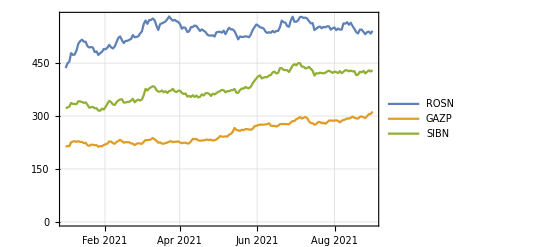

```mathematica
DateListPlot[{rosn,gazp,sibn},{{2021,1,1},{2021,8,31}},PlotRange->All, GridLines->Automatic,Frame->True,PlotLegends->{"ROSN","GAZP","SIBN"}]
```

#### Построение попарного распределения логарифмических доходностей

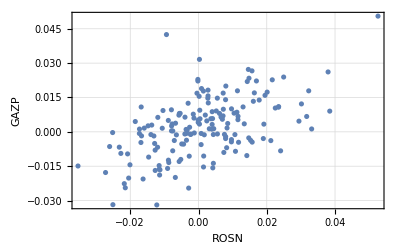

```mathematica
unionROSNGAZP=Table[{ROSN[[i]],GAZP[[i]]},{i,Length[GAZP]}];
ListPlot[unionROSNGAZP,PlotRange->All, GridLines->Automatic,Frame->True,AxesLabel->{"ROSN","GAZP"}]
```

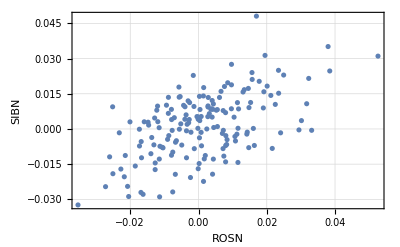

```mathematica
unionROSNSIBN=Table[{ROSN[[i]],SIBN[[i]]},{i,Length[GAZP]}];
ListPlot[unionROSNSIBN,PlotRange->All, GridLines->Automatic,Frame->True,AxesLabel->{"ROSN","SIBN"}]
```

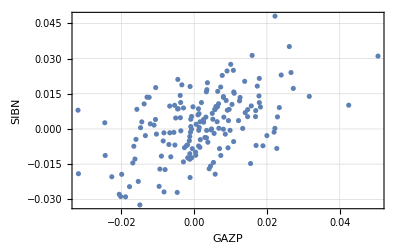

```mathematica
unionGAZPSIBN=Table[{GAZP[[i]],SIBN[[i]]},{i,Length[GAZP]}];
ListPlot[unionGAZPSIBN,PlotRange->All, GridLines->Automatic,Frame->True,AxesLabel->{"GAZP","SIBN"}]
```

#### Построим графики псевдо-наблюдений

```mathematica
T=Length[GAZP];
```

```mathematica
psROSN={};
psGAZP={};
psSIBN={};
```

```mathematica
For[i=1,i<=T,i++,
f = 1/(1+T)*Sum[If[ROSN[[j]]<ROSN[[i]],1,0],{j,T}];
AppendTo[psROSN,f]
]
```

```mathematica
For[i=1,i<=T,i++,
f = 1/(1+T)*Sum[If[GAZP[[j]]<GAZP[[i]],1,0],{j,T}];
AppendTo[psGAZP,f]
]
```

```mathematica
For[i=1,i<=T,i++,
f = 1/(1+T)*Sum[If[SIBN[[j]]<SIBN[[i]],1,0],{j,T}];
AppendTo[psSIBN,f]
]
```

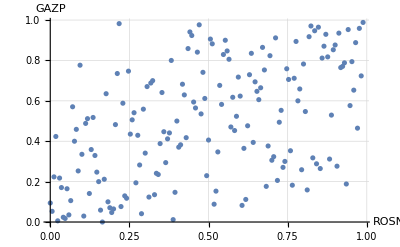

```mathematica
unionpsROSNpsGAZP=Table[{psROSN[[i]],psGAZP[[i]]},{i,Length[GAZP]}];
ListPlot[unionpsROSNpsGAZP,PlotRange->All, GridLines->Automatic,AxesLabel->{"ROSN","GAZP"}]
```

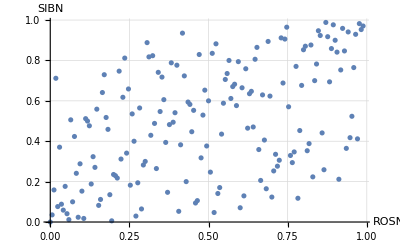

```mathematica
unionpsROSNpsSIBN=Table[{psROSN[[i]],psSIBN[[i]]},{i,Length[GAZP]}];
ListPlot[unionpsROSNpsSIBN,PlotRange->All, GridLines->Automatic,AxesLabel->{"ROSN","SIBN"}]
```

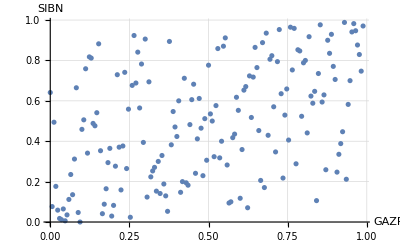

```mathematica
unionpsGAZPpsSIBN=Table[{psGAZP[[i]],psSIBN[[i]]},{i,Length[GAZP]}];
ListPlot[unionpsGAZPpsSIBN,PlotRange->All, GridLines->Automatic,AxesLabel->{"GAZP","SIBN"}]
```

#### Выбор маргинальных распределений

Для описания логарифмических доходностей финансовых временных рядов в качестве кандитатов были рассмотрены следующие четырех-параметрические распределения:
	1) Гиперболическое. 
	2) Устойчивое.
	3) Мейкснера.

Гиперболическое распределение

```mathematica
paramsForGAZP1=FindDistributionParameters[GAZP,HyperbolicDistribution[θ,ξ,δ,μ],ParameterEstimator->"MaximumLikelihood"]
paramsForROSN1=FindDistributionParameters[ROSN,HyperbolicDistribution[θ,ξ,δ,μ],ParameterEstimator->"MaximumLikelihood"]
paramsForSIBN1=FindDistributionParameters[SIBN,HyperbolicDistribution[θ,ξ,δ,μ],ParameterEstimator->"MaximumLikelihood"]
```

{θ→152.398,ξ→6.78381,δ→0.0149069,μ→0.00114595}

{θ→5289.47,ξ→5227.79,δ→1.30058×10^-7,μ→-0.0148334}

{θ→208.999,ξ→-16.5232,δ→0.0312237,μ→0.00476403}

CramerVonMisesTest

```mathematica
CramerVonMisesTest[GAZP,HyperbolicDistribution[θ,ξ,δ,μ]/.paramsForGAZP1]
CramerVonMisesTest[ROSN,HyperbolicDistribution[θ,ξ,δ,μ]/.paramsForROSN1]
CramerVonMisesTest[SIBN,HyperbolicDistribution[θ,ξ,δ,μ]/.paramsForSIBN1]
```

0.992278

0.00131895

0.972686

KolmogorovSmirnovTest[]

```mathematica
KolmogorovSmirnovTest[GAZP,HyperbolicDistribution[θ,ξ,δ,μ]/.paramsForGAZP1]
KolmogorovSmirnovTest[ROSN,HyperbolicDistribution[θ,ξ,δ,μ]/.paramsForROSN1]
KolmogorovSmirnovTest[SIBN,HyperbolicDistribution[θ,ξ,δ,μ]/.paramsForSIBN1]
```

0.955347

0.000611271

0.890167

Устойчивое распределение

```mathematica
paramsForGAZP2=FindDistributionParameters[GAZP,StableDistribution[θ,ξ,δ,μ],ParameterEstimator->"MaximumLikelihood"]
paramsForROSN2=FindDistributionParameters[ROSN,StableDistribution[θ,ξ,δ,μ],ParameterEstimator->"MaximumLikelihood"]
paramsForSIBN2=FindDistributionParameters[SIBN,StableDistribution[θ,ξ,δ,μ],ParameterEstimator->"MaximumLikelihood"]
```

{θ→1.94102,ξ→1.,δ→0.00236373,μ→0.0087781}

{θ→1.90515,ξ→1.,δ→0.00155318,μ→0.00964014}

{θ→2.,ξ→-1.,δ→0.00169767,μ→0.00965453}

CramerVonMisesTest

```mathematica
CramerVonMisesTest[GAZP,StableDistribution[θ,ξ,δ,μ]/.paramsForGAZP2]
CramerVonMisesTest[ROSN,StableDistribution[θ,ξ,δ,μ]/.paramsForROSN2]
CramerVonMisesTest[SIBN,StableDistribution[θ,ξ,δ,μ]/.paramsForSIBN2]
```

```mathematica
0.8407041736867273
```

0.99991

0.893989

KolmogorovSmirnovTest[]

```mathematica
KolmogorovSmirnovTest[GAZP,StableDistribution[θ,ξ,δ,μ]/.paramsForGAZP2]
KolmogorovSmirnovTest[ROSN,StableDistribution[θ,ξ,δ,μ]/.paramsForROSN2]
KolmogorovSmirnovTest[SIBN,StableDistribution[θ,ξ,δ,μ]/.paramsForSIBN2]
```

0.679894

0.996486

0.936454

Распределение Мейкснера

```mathematica
paramsForGAZP3=FindDistributionParameters[GAZP,MeixnerDistribution[θ,ξ,δ,μ],ParameterEstimator->"MaximumLikelihood"]
paramsForROSN3=FindDistributionParameters[ROSN,MeixnerDistribution[θ,ξ,δ,μ],ParameterEstimator->"MaximumLikelihood"]
paramsForSIBN3=FindDistributionParameters[SIBN,MeixnerDistribution[θ,ξ,δ,μ],ParameterEstimator->"MaximumLikelihood"]
```

{θ→0.0188662,ξ→0.129751,δ→0.00113238,μ→0.939228}

{θ→0.0092247,ξ→1.03266,δ→-0.0177628,μ→3.63685}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{θ→0.00794506,ξ→0.161851,δ→-0.00207676,μ→5.85762}

CramerVonMisesTest

```mathematica
CramerVonMisesTest[GAZP,MeixnerDistribution[θ,ξ,δ,μ]/.paramsForGAZP3]
CramerVonMisesTest[ROSN,MeixnerDistribution[θ,ξ,δ,μ]/.paramsForROSN3]
CramerVonMisesTest[SIBN,MeixnerDistribution[θ,ξ,δ,μ]/.paramsForSIBN3]
```

0.991911

0.997947

0.870109

KolmogorovSmirnovTest[]

```mathematica
KolmogorovSmirnovTest[GAZP,MeixnerDistribution[θ,ξ,δ,μ]/.paramsForGAZP3]
KolmogorovSmirnovTest[ROSN,MeixnerDistribution[θ,ξ,δ,μ]/.paramsForROSN3]
KolmogorovSmirnovTest[SIBN,MeixnerDistribution[θ,ξ,δ,μ]/.paramsForSIBN3]
```

0.953946

0.95636

0.853347

#### Построение гистограмм логарифмических доходностей акций

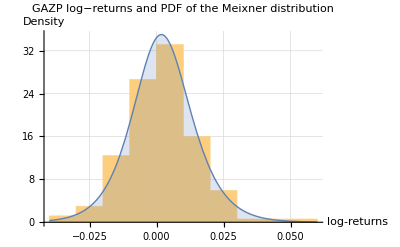

```mathematica
Show[Histogram[GAZP,10,"PDF"],Plot[PDF[MeixnerDistribution[θ,ξ,δ,μ]/.paramsForGAZP3,x], {x,-0.04,0.06},PlotStyle->Thick,Filling->Axis], AxesLabel->{"log-returns","Density"}, GridLines->Automatic,Exclusions->None, PlotLabel->"GAZP log−returns and
PDF of the Meixner distribution"]
```

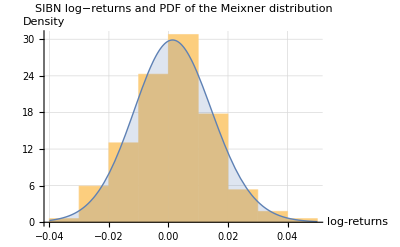

```mathematica
Show[Histogram[SIBN,10,"PDF"],Plot[PDF[MeixnerDistribution[θ,ξ,δ,μ]/.paramsForSIBN3,x],{x,-0.04,0.05},PlotStyle->Thick,Filling->Axis], GridLines->Automatic, PlotLabel->"SIBN log−returns and
PDF of the Meixner distribution",Exclusions->None, AxesLabel->{"log-returns","Density"}]
```

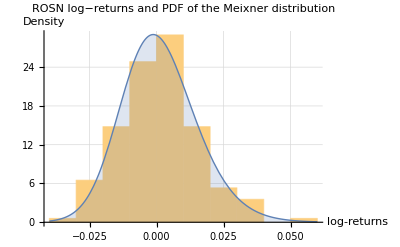

```mathematica
Show[Histogram[ROSN,10,"PDF"],Plot[PDF[MeixnerDistribution[θ,ξ,δ,μ]/.paramsForROSN3,x],{x,-0.04,0.06},PlotStyle->Thick,Filling->Axis], GridLines->Automatic, PlotLabel->"ROSN log−returns and
PDF of the Meixner distribution",Exclusions->None, AxesLabel->{"log-returns","Density"}]
```

#### Задание маргинальных распределений с заданными параметрами

```mathematica
gazpDistribution=MeixnerDistribution[θ,ξ,δ,μ]/.paramsForGAZP3;
sibnDistribution=MeixnerDistribution[θ,ξ,δ,μ]/.paramsForSIBN3;
rosnDistribution=MeixnerDistribution[θ,ξ,δ,μ]/.paramsForROSN3;
```

#### Оценка параметров копулярных моделей Гаусса и Стьюдента

```mathematica
paramsModel=KendallTau[Transpose[{psGAZP,psROSN,psSIBN}]]
```

{{1,2453/7098,56/169},{2453/7098,1,823/2366},{56/169,823/2366,1}}

Формируем куполы Гаусса и Стьюдента

```mathematica
GaussCopula=CopulaDistribution[{"Multinormal",paramsModel},{gazpDistribution,rosnDistribution,sibnDistribution}];
StudentCopula =CopulaDistribution[{"MultivariateT",paramsModel,3},{gazpDistribution,rosnDistribution,sibnDistribution}];
```

#### Перейдем к двумерным копулам и к построению графиков

Гауссова копула

```mathematica
param1=KendallTau[Transpose[{psGAZP,psROSN}]];
param2=KendallTau[Transpose[{psGAZP,psSIBN}]];
param3=KendallTau[Transpose[{psROSN,psSIBN}]];
```

```mathematica
GaussCopulaGAZPROSN=CopulaDistribution[{"Multinormal",param1},{gazpDistribution,rosnDistribution}];
GaussCopulaGAZPSIBN=CopulaDistribution[{"Multinormal",param2},{gazpDistribution,sibnDistribution}];
GaussCopulaROSNSIBN=CopulaDistribution[{"Multinormal",param3},{rosnDistribution,sibnDistribution}];
```

```mathematica
Plot3D[PDF[GaussCopulaGAZPROSN,{x,y}]//Evaluate,{x,-0.2,0.2},{y,-0.2,0.2},PlotRange->All,PlotLabel->"GAZP\ROSN"]
```

-Graphics3D-

```mathematica
Plot3D[PDF[GaussCopulaGAZPSIBN,{x,y}]//Evaluate,{x,-0.2,0.2},{y,-0.2,0.2},PlotRange->All,PlotLabel->"GAZP\SIBN"]
```

-Graphics3D-

```mathematica
Plot3D[PDF[GaussCopulaROSNSIBN,{x,y}]//Evaluate,{x,-0.2,0.2},{y,-0.2,0.2},PlotRange->All,PlotLabel->"ROSN\SIBN"]
```

-Graphics3D-

Копула Стьюдента

```mathematica
StudentCopulaGAZPROSN=CopulaDistribution[{"MultivariateT",param1,3},{gazpDistribution,rosnDistribution}];
StudentCopulaGAZPSIBN=CopulaDistribution[{"MultivariateT",param2,3},{gazpDistribution,sibnDistribution}];
StudentCopulaROSNSIBN=CopulaDistribution[{"MultivariateT",param3,3},{rosnDistribution,sibnDistribution}];
```

```mathematica
Plot3D[PDF[StudentCopulaGAZPROSN,{x,y}]//Evaluate,{x,-0.2,0.2},{y,-0.2,0.2},PlotRange->All,PlotLabel->"GAZP\ROSN"]
```

-Graphics3D-

```mathematica
Plot3D[PDF[StudentCopulaGAZPSIBN,{x,y}]//Evaluate,{x,-0.1,0.1},{y,-0.1,0.1},PlotRange->All,PlotLabel->"GAZP\SIBN"]
```

-Graphics3D-

```mathematica
Plot3D[PDF[StudentCopulaROSNSIBN,{x,y}]//Evaluate,{x,-0.1,0.1},{y,-0.1,0.1},PlotRange->All,PlotLabel->"ROSN\SIBN"]
```

-Graphics3D-

#### Моделирование выборки с помощью полученных распределений

```mathematica
sampleGauss=RandomVariate[GaussCopula,500];
sampleStudent=RandomVariate[StudentCopula,500];
```

```mathematica
KolmogorovSmirnovTest[LogData,sampleGauss]
KolmogorovSmirnovTest[LogData,sampleStudent]
```

0.409659

0.219329

```mathematica
CramerVonMisesTest[LogData,sampleGauss]
CramerVonMisesTest[LogData,sampleStudent]
```

0.493943

0.282754

```mathematica
sampleGauss=RandomVariate[GaussCopula,500];
sampleStudent=RandomVariate[StudentCopula,500];
```

```mathematica
KolmogorovSmirnovTest[LogData,sampleGauss]
KolmogorovSmirnovTest[LogData,sampleStudent]
```

0.363301

0.563765

```mathematica
CramerVonMisesTest[LogData,sampleGauss]
CramerVonMisesTest[LogData,sampleStudent]
```

0.450748

0.492793

```mathematica
sampleGauss=RandomVariate[GaussCopula,500];
sampleStudent=RandomVariate[StudentCopula,500];
```

```mathematica
KolmogorovSmirnovTest[LogData,sampleGauss]
KolmogorovSmirnovTest[LogData,sampleStudent]
```

0.457918

0.554559

```mathematica
CramerVonMisesTest[LogData,sampleGauss]
CramerVonMisesTest[LogData,sampleStudent]
```

0.422278

0.482061